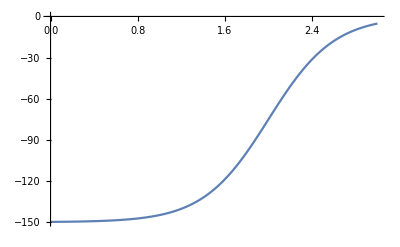

```mathematica
Subscript[m, N]=940;ℏc=197.327;
V0=150;R=2;a=0.3;μ=8/9 Subscript[m, N];
rmax=3;dr=0.01;
rlist=Range[0,rmax,dr];
len=Length[rlist];
V[r_]:=-V0/(1+Exp[(r-R)/a]);
Vmat=DiagonalMatrix[V[rlist]];
ListLinePlot[V[rlist],DataRange->{0,rmax}]
```

```mathematica
(*calculate Hamiltonian matrix and eigensystem*)
one[n_,d_]:=
DiagonalMatrix[1+0Range[n-Abs[d]],d];
H0=Vmat+-ℏc^2/(2 μ) 1/dr^2(one[len,-1]-2 one[len,0]+one[len,1]);
k[En_]:=Sqrt[-(2μ En)/ℏc^2];
B[En_]:=1-dr k[En];
Hnew[En_]:=(H=H0;H[[len,len]]=Vmat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(-2+B[En]);H)
eigenv[{En_,i_}]:=(eval=Sort[Eigenvalues[Hnew[En]]];{eval[[i]],i})
```

```mathematica
ϵ=10^-10;
n=1;
evals=List[];
```

```mathematica
En=NestWhileList[eigenv,{-V0/2,n},Abs[#1[[1]]-#2[[1]]]>ϵ&,2,10][[-1,1]]
While[Re[En]<0,
evals=Append[evals,En];n++;En=NestWhileList[eigenv,{-V0/2,n},Abs[#1[[1]]-#2[[1]]]>ϵ&,2,10][[-1,1]];]
```

```mathematica
eigenVector[i_]:=NullSpace[Hnew[evals[[i]]]-evals[[i]] IdentityMatrix[len]]
```

```mathematica
eigenVector[1];
```

```mathematica
eigenVector[2]
```

{}

```mathematica
Hnew[evals[[1]]].eigenVector[1]-evals[[1]] eigenVector[1]//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.04752×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.0081×10^-10,0,0,0,0,0,0,0,0,0,0,1.2702×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.06072×10^-10,-1.23547×10^-10,0,0,0,0,0,0,0,0,-1.07805×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.53126×10^-10,0,0,0,0,0,-1.13381×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.2138×10^-10,0,0,0,0,-1.20669×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.01817×10^-10,0,0,0,0,0,0,0,0,0,-1.65558×10^-10,0,-1.11023×10^-10,0,0,0,0,0,0,0,0,1.00285×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.37984×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,-1.12912×10^-10,0,-1.04329×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
{eval,evec}={eval,evec}[[All,Position[{eval,evec}[[1,All]],_?(#<0&)][[All,1]]]];
```

```mathematica
(*En=NestWhileList[SetPrecision[eigenv,5]{-V0,1},UnsameQ,2,100]*)
(*FindRoot[eigenv[{x,1}][[1]]==x,{x,-V0/2,-V0,0},WorkingPrecision->2]*)
(*Plot[{eigenv[{x,n}][[1]],#&[x]},{x,-V0,0}]*)
```

```mathematica
wave[En_,r_]:=Exp[-k[En] r];
const[i_]:=evec[[i,-1]]/wave[eval[[i]],rmax];
rmaxx=10.;
Manipulate[ListLinePlot[{Transpose[{rlist,evec⟦i⟧}],Transpose[{Range[rmax,rmaxx,dr],const[i] wave[eval[[i]],Range[rmax,rmaxx,dr]]}]},PlotRange->All],{i,1,Length[eval],1}]
```

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {rlist,evec⟦1⟧} cannot be transposed.

Range::range: Range specification in Range[rmax,rmaxx,dr] does not have appropriate bounds.

Part::partd: Part specification eval⟦1⟧ is longer than depth of object.

Range::range: Range specification in Range[rmax,rmaxx,dr] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[rmax,rmaxx,dr],const[1] wave[eval⟦1⟧,Range[rmax,rmaxx,dr]]} cannot be transposed.

Transpose::nmtx: The first two levels of {Range[rmax,rmaxx,dr],const[1.] wave[eval⟦1⟧,Range[rmax,rmaxx,dr]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {rlist,evec⟦1⟧} cannot be transposed.

Range::range: Range specification in Range[rmax,rmaxx,dr] does not have appropriate bounds.

Part::partd: Part specification eval⟦1⟧ is longer than depth of object.

Range::range: Range specification in Range[rmax,rmaxx,dr] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[rmax,rmaxx,dr],const[1] wave[eval⟦1⟧,Range[rmax,rmaxx,dr]]} cannot be transposed.

Transpose::nmtx: The first two levels of {Range[rmax,rmaxx,dr],const[1.] wave[eval⟦1⟧,Range[rmax,rmaxx,dr]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«251»},«1»} cannot be transposed.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Part::partd: Part specification eval⟦1⟧ is longer than depth of object.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[3,rmaxx,0.01],const[1] wave[eval⟦1⟧,Range[3,rmaxx,0.01]]} cannot be transposed.

Range::range: Range specification in Range[3.,rmaxx,0.01] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[3.,rmaxx,0.01],const[1.] wave[eval⟦1⟧,Range[3.,rmaxx,0.01]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«251»},«1»} cannot be transposed.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[3,rmaxx,0.01],const[1] wave[931909.,Range[3,rmaxx,0.01]]} cannot be transposed.

Range::range: Range specification in Range[3.,rmaxx,0.01] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[3.,rmaxx,0.01],const[1.] wave[931909.,Range[3.,rmaxx,0.01]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«251»},«1»} cannot be transposed.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[3,rmaxx,0.01],const[1] wave[-98.6551+0.00835231 ⅈ,Range[3,rmaxx,0.01]]} cannot be transposed.

Range::range: Range specification in Range[3.,rmaxx,0.01] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[3.,rmaxx,0.01],const[1.] wave[-98.6551+0.00835231 ⅈ,Range[3.,rmaxx,0.01]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«251»},«1»} cannot be transposed.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[3,rmaxx,0.01],const[1] wave[-99.0708,Range[3,rmaxx,0.01]]} cannot be transposed.

Range::range: Range specification in Range[3.,rmaxx,0.01] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[3.,rmaxx,0.01],const[1.] wave[-99.0708,Range[3.,rmaxx,0.01]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«251»},«1»} cannot be transposed.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[3,rmaxx,0.01],const[1] wave[-99.2895,Range[3,rmaxx,0.01]]} cannot be transposed.

Range::range: Range specification in Range[3.,rmaxx,0.01] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[3.,rmaxx,0.01],const[1.] wave[-99.2895,Range[3.,rmaxx,0.01]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«251»},«1»} cannot be transposed.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[3,rmaxx,0.01],const[1] wave[-99.0708,Range[3,rmaxx,0.01]]} cannot be transposed.

Range::range: Range specification in Range[3.,rmaxx,0.01] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[3.,rmaxx,0.01],const[1.] wave[-99.0708,Range[3.,rmaxx,0.01]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«251»},«1»} cannot be transposed.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[3,rmaxx,0.01],const[1] wave[-99.2895,Range[3,rmaxx,0.01]]} cannot be transposed.

Range::range: Range specification in Range[3.,rmaxx,0.01] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[3.,rmaxx,0.01],const[1.] wave[-99.2895,Range[3.,rmaxx,0.01]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«251»},«1»} cannot be transposed.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[3,rmaxx,0.01],const[1] wave[-99.2895,Range[3,rmaxx,0.01]]} cannot be transposed.

Range::range: Range specification in Range[3.,rmaxx,0.01] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[3.,rmaxx,0.01],const[1.] wave[-99.2895,Range[3.,rmaxx,0.01]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«251»},«1»} cannot be transposed.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[3,rmaxx,0.01],const[1] wave[-99.2895,Range[3,rmaxx,0.01]]} cannot be transposed.

Range::range: Range specification in Range[3.,rmaxx,0.01] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[3.,rmaxx,0.01],const[1.] wave[-99.2895,Range[3.,rmaxx,0.01]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«251»},«1»} cannot be transposed.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[3,rmaxx,0.01],const[1] wave[-99.0605+0.3549 ⅈ,Range[3,rmaxx,0.01]]} cannot be transposed.

Range::range: Range specification in Range[3.,rmaxx,0.01] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[3.,rmaxx,0.01],const[1.] wave[-99.0605+0.3549 ⅈ,Range[3.,rmaxx,0.01]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«251»},«1»} cannot be transposed.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[3,rmaxx,0.01],const[1] wave[-98.8923+0.33329 ⅈ,Range[3,rmaxx,0.01]]} cannot be transposed.

Range::range: Range specification in Range[3.,rmaxx,0.01] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[3.,rmaxx,0.01],const[1.] wave[-98.8923+0.33329 ⅈ,Range[3.,rmaxx,0.01]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«251»},«1»} cannot be transposed.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[3,rmaxx,0.01],const[1] wave[-99.2895,Range[3,rmaxx,0.01]]} cannot be transposed.

Range::range: Range specification in Range[3.,rmaxx,0.01] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[3.,rmaxx,0.01],const[1.] wave[-99.2895,Range[3.,rmaxx,0.01]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«251»},«1»} cannot be transposed.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[3,rmaxx,0.01],const[1] wave[-99.2895,Range[3,rmaxx,0.01]]} cannot be transposed.

Range::range: Range specification in Range[3.,rmaxx,0.01] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[3.,rmaxx,0.01],const[1.] wave[-99.2895,Range[3.,rmaxx,0.01]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«251»},«1»} cannot be transposed.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Part::partw: Part 1 of {} does not exist.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[3,rmaxx,0.01],const[1] wave[{}⟦1⟧,Range[3,rmaxx,0.01]]} cannot be transposed.

Range::range: Range specification in Range[3.,rmaxx,0.01] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[3.,rmaxx,0.01],const[1.] wave[{}⟦1⟧,Range[3.,rmaxx,0.01]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«251»},«1»} cannot be transposed.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[3,rmaxx,0.01],const[1] wave[-99.0605+0.3549 ⅈ,Range[3,rmaxx,0.01]]} cannot be transposed.

Range::range: Range specification in Range[3.,rmaxx,0.01] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[3.,rmaxx,0.01],const[1.] wave[-99.0605+0.3549 ⅈ,Range[3.,rmaxx,0.01]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«251»},«1»} cannot be transposed.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[3,rmaxx,0.01],const[1] wave[-98.8923+0.33329 ⅈ,Range[3,rmaxx,0.01]]} cannot be transposed.

Range::range: Range specification in Range[3.,rmaxx,0.01] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[3.,rmaxx,0.01],const[1.] wave[-98.8923+0.33329 ⅈ,Range[3.,rmaxx,0.01]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«251»},«1»} cannot be transposed.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[3,rmaxx,0.01],const[1] wave[-99.0708,Range[3,rmaxx,0.01]]} cannot be transposed.

Range::range: Range specification in Range[3.,rmaxx,0.01] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[3.,rmaxx,0.01],const[1.] wave[-99.0708,Range[3.,rmaxx,0.01]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«251»},«1»} cannot be transposed.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[3,rmaxx,0.01],const[1] wave[-99.2895,Range[3,rmaxx,0.01]]} cannot be transposed.

Range::range: Range specification in Range[3.,rmaxx,0.01] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[3.,rmaxx,0.01],const[1.] wave[-99.2895,Range[3.,rmaxx,0.01]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«251»},«1»} cannot be transposed.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Part::partd: Part specification eval⟦1⟧ is longer than depth of object.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[3,rmaxx,0.01],const[1] wave[eval⟦1⟧,Range[3,rmaxx,0.01]]} cannot be transposed.

Range::range: Range specification in Range[3.,rmaxx,0.01] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[3.,rmaxx,0.01],const[1.] wave[eval⟦1⟧,Range[3.,rmaxx,0.01]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«251»},«1»} cannot be transposed.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[3,rmaxx,0.01],const[1] wave[-99.2895,Range[3,rmaxx,0.01]]} cannot be transposed.

Range::range: Range specification in Range[3.,rmaxx,0.01] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[3.,rmaxx,0.01],const[1.] wave[-99.2895,Range[3.,rmaxx,0.01]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«251»},«1»} cannot be transposed.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[3,rmaxx,0.01],const[1] wave[-99.0605+0.3549 ⅈ,Range[3,rmaxx,0.01]]} cannot be transposed.

Range::range: Range specification in Range[3.,rmaxx,0.01] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[3.,rmaxx,0.01],const[1.] wave[-99.0605+0.3549 ⅈ,Range[3.,rmaxx,0.01]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«251»},«1»} cannot be transposed.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[3,rmaxx,0.01],const[1] wave[-99.0605+0.3549 ⅈ,Range[3,rmaxx,0.01]]} cannot be transposed.

Range::range: Range specification in Range[3.,rmaxx,0.01] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[3.,rmaxx,0.01],const[1.] wave[-99.0605+0.3549 ⅈ,Range[3.,rmaxx,0.01]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«251»},«1»} cannot be transposed.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Part::partw: Part 1 of {} does not exist.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[3,rmaxx,0.01],const[1] wave[{}⟦1⟧,Range[3,rmaxx,0.01]]} cannot be transposed.

Range::range: Range specification in Range[3.,rmaxx,0.01] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[3.,rmaxx,0.01],const[1.] wave[{}⟦1⟧,Range[3.,rmaxx,0.01]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«251»},«1»} cannot be transposed.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[3,rmaxx,0.01],const[1] wave[-99.0605+0.3549 ⅈ,Range[3,rmaxx,0.01]]} cannot be transposed.

Range::range: Range specification in Range[3.,rmaxx,0.01] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[3.,rmaxx,0.01],const[1.] wave[-99.0605+0.3549 ⅈ,Range[3.,rmaxx,0.01]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«251»},«1»} cannot be transposed.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[3,rmaxx,0.01],const[1] wave[94.1727+35.965 ⅈ,Range[3,rmaxx,0.01]]} cannot be transposed.

Range::range: Range specification in Range[3.,rmaxx,0.01] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[3.,rmaxx,0.01],const[1.] wave[94.1727+35.965 ⅈ,Range[3.,rmaxx,0.01]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«251»},«1»} cannot be transposed.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[3,rmaxx,0.01],const[1] wave[-98.8923+0.33329 ⅈ,Range[3,rmaxx,0.01]]} cannot be transposed.

Range::range: Range specification in Range[3.,rmaxx,0.01] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[3.,rmaxx,0.01],const[1.] wave[-98.8923+0.33329 ⅈ,Range[3.,rmaxx,0.01]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«251»},«1»} cannot be transposed.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[3,rmaxx,0.01],const[1] wave[-98.809+0.289295 ⅈ,Range[3,rmaxx,0.01]]} cannot be transposed.

Range::range: Range specification in Range[3.,rmaxx,0.01] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[3.,rmaxx,0.01],const[1.] wave[-98.809+0.289295 ⅈ,Range[3.,rmaxx,0.01]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«251»},«1»} cannot be transposed.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[3,rmaxx,0.01],const[1] wave[-99.0605+0.3549 ⅈ,Range[3,rmaxx,0.01]]} cannot be transposed.

Range::range: Range specification in Range[3.,rmaxx,0.01] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[3.,rmaxx,0.01],const[1.] wave[-99.0605+0.3549 ⅈ,Range[3.,rmaxx,0.01]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«251»},«1»} cannot be transposed.

Range::range: Range specification in Range[3,rmaxx,0.01] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[3,rmaxx,0.01],const[1] wave[-99.0605+0.3549 ⅈ,Range[3,rmaxx,0.01]]} cannot be transposed.

Range::range: Range specification in Range[3.,rmaxx,0.01] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[3.,rmaxx,0.01],const[1.] wave[-99.0605+0.3549 ⅈ,Range[3.,rmaxx,0.01]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.